# Coil Examples

## Examples from Designing optimal loop, saddle, and ellipse-based magnetic coils by spherical harmonic mapping

Import the package:

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "CodeBase", "CreateCoilDiscrete.wl"}]]
```

## General Information

Each function has a usage message, for example:

-Graphics-

The FindLoopCoil, FindSaddleCoil and FindEllipseCoil functions take a “PrintSteps” option which can be used to interrogate their harmonic expressions and search meshes.

Timings can be computed via the AbsoluteTiming or RepeatedTiming functions. E.g.:

```mathematica
AbsoluteTiming[FindLoopCoil[{1,1},1,{.1,2},"CoilsReturned"->1]]
```

{0.563457,{{Coilχc[1]→0.384385,Coilχc[2]→1.05207,DesToErr→18.1046}}}

### Options

Default option values can be found via Options[func]:

```mathematica
Options[FindLoopCoil]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision,CoilsReturned→10,ValuesOnly→False,NulledHarmonics→Automatic,LeadingErrorHarmonic→Automatic,MeshPointsPerχc→20,DuplicatesProximity→Scaled[0.03],NullingThreshold→0.00001,MinSeparationsDifference→Scaled[0.01],ExpansionPointsPerContourDim→Automatic,ContourMeshNN→Automatic,ExpansionBleed→1.5,Seed→1,PrintSteps→False,FinalSolutionChecks→False}

Many of these options are coming from FindRoot. To find the bespoke options, take the complement with FindRoot’s options:

```mathematica
Complement[Options[FindLoopCoil], Options[FindRoot]]
```

{CoilsReturned→10,ContourMeshNN→Automatic,DuplicatesProximity→Scaled[0.03],ExpansionBleed→1.5,ExpansionPointsPerContourDim→Automatic,FinalSolutionChecks→False,LeadingErrorHarmonic→Automatic,MeshPointsPerχc→20,MinSeparationsDifference→Scaled[0.01],NulledHarmonics→Automatic,NullingThreshold→0.00001,PrintSteps→False,Seed→1,ValuesOnly→False}

## Loops

### Simple example: Helmholtz pair

Firstly, let’s optimize a Helmholtz pair consisting of a simple turn of radius ρc = 1 m carrying one amp of current generating the N=1 field harmonic existing between dc = 0 to dc = ρc.

```mathematica
solutions =FindLoopCoil[{1},1, {0.01, 1}]
```

{{Coilχc[1]→0.5,DesToErr→8.311}}

### B_(2,0)

Let us optimize loops to generate the B_(2,0)field harmonic. First let’s examine what the B_x,B_y,and B_z components of this field harmonic are along the x-, y-, and z-axes.

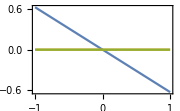
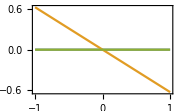
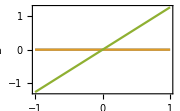

```mathematica
order = 2; (* Desired harmonic order *)
degree = 0; (* Desired harmonic degree *)
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
```

Let us define the known variables in our optimization of loop coils.

```mathematica
curr = {1, -2, 2}; (* Turn ratios (A) *)
χcmin = .1; (* Minimum normalized separation *)
χcmax = √3/2; (* Maximum normalized separation *)
ρc = 10 1*^-2; (* Coil radius (m) *)
```

We will now select the optimal positions of loops to maximize the N=2, M=0 field harmonic.

```mathematica
solutions =FindLoopCoil[curr,order, {χcmin, χcmax}]
```

{{Coilχc[1]→0.554372,Coilχc[2]→0.674766,Coilχc[3]→0.866025,DesToErr→34.5198},{Coilχc[1]→0.5531,Coilχc[2]→0.673608,Coilχc[3]→0.865142,DesToErr→33.5852},{Coilχc[1]→0.552599,Coilχc[2]→0.673065,Coilχc[3]→0.864629,DesToErr→33.2277},{Coilχc[1]→0.551441,Coilχc[2]→0.671812,Coilχc[3]→0.863445,DesToErr→32.4277},{Coilχc[1]→0.549406,Coilχc[2]→0.669616,Coilχc[3]→0.861379,DesToErr→31.1048},{Coilχc[1]→0.549032,Coilχc[2]→0.669214,Coilχc[3]→0.861001,DesToErr→30.8729},{Coilχc[1]→0.547837,Coilχc[2]→0.66793,Coilχc[3]→0.859797,DesToErr→30.1515},{Coilχc[1]→0.546613,Coilχc[2]→0.666618,Coilχc[3]→0.858569,DesToErr→29.4437},{Coilχc[1]→0.545779,Coilχc[2]→0.665726,Coilχc[3]→0.857737,DesToErr→28.9793},{Coilχc[1]→0.543812,Coilχc[2]→0.663628,Coilχc[3]→0.855782,DesToErr→27.9345}}

We have identified the ten coils which null the N=4 and N=6 field harmonics while maximizing the strength of the desired field harmonic compared to that of the leading-order error. In this case, DesToErr, is the magnitude of the desired field harmonic of order N=2 divided by the magnitude of the leading-order error field harmonic of order N=8.

We select the set of loops which maximize the value of this ratio:

```mathematica
χcopt ={Coilχc[1],Coilχc[2],Coilχc[3]} /. solutions[[1]]
```

{0.554372,0.674766,0.866025}

Let’s create a plot of the optimal set of loops on the surface of the coil cylinder.

```mathematica
LoopCoilPlot[χcopt,curr, ρc,order]
```

Let’s examine the B_x,B_y,and B_zcomponents of the magnetic field along the x-, y-, and z-axes.

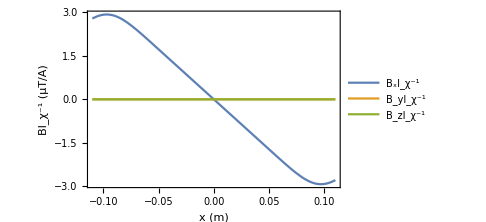
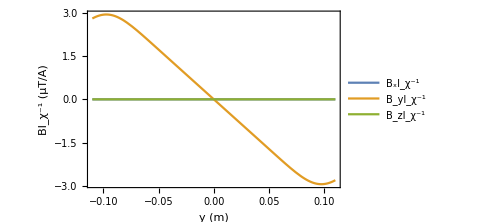
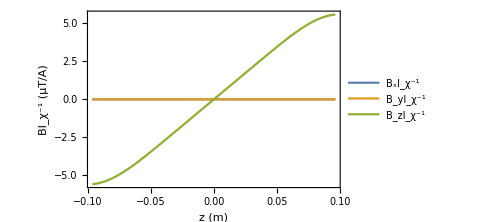

```mathematica
LoopFieldPlot[χcopt,curr, ρc,order]
```

We can also plot the B_x,B_y,and B_zcomponents of the magnetic field generated by the coils along the xz-plane. We’ll modify the plot range so we only display the values of the field between [–6, 6] µT.

```mathematica
LoopFieldPlot2D[χcopt,curr, ρc,order, PlotRange->{Full,Full,{-6,6}}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Optimization Steps

Print the evaluation steps.

```mathematica
allsolutions=FindLoopCoil[curr,order, {χcmin, χcmax},"PrintSteps"->True,"CoilsReturned"->All];
```

Total desired harmonic

Total nulled harmonics

Total leading error harmonic

FindRoot function

Initial (coarse) mesh

Initial solutions (raw)

Initial solutions (filtered)

Contour Mesh

Final solutions (unfiltered)

Extract the numeric points by taking parts, for example:

```mathematica
rawseparations=[[All,All,-1]];
Short[rawseparations,5] (* Short is used to reduce the expression to a few lines *)
```

{{0.1,0.185114,0.270228},{0.1,0.185114,0.355342},«116»,{0.610684,0.780911,0.866025},{0.695798,0.780911,0.866025}}

Let’s plot the initial solutions:

```mathematica
ListPointPlot3D[rawseparations,AxesLabel->Flatten[Text[#]&/@{"χ_c1","χ_c1","χ_c3"}]]
```

-Graphics3D-

Now let’s plot all stages of the optimization.

```mathematica
Row[
Labeled[ListPointPlot3D[#1,ImageSize->300,AxesLabel->Flatten[Text[#]&/@{"χ_c1","χ_c1","χ_c3"}]],#2]&@@@{
{[[All,All,-1]],Text["Initial solutions (raw)"]},
{,Text["Initial solutions (filtered)"]},
{,Text["Contour mesh"]},
{allsolutions[[All,1;;3,-1]],Text["Final solutions"]},
}]
```

-Graphics3D-Initial solutions (raw)-Graphics3D-Initial solutions (filtered)-Graphics3D-Contour mesh-Graphics3D-Final solutions

Finally, let’s colour the final solutions by desired-to-leading-order-error ratio:

```mathematica
Module[{minMax,cols,lookup,colFn},
minMax=MinMax[allsolutions[[All,-1,-1]]];
(* Construct the first argument of Blend. Use a log scaling. *)
cols=Transpose[{Log10[minMax],{Blue,Red}}];
(* Construct a dictionary of sol1 -> ratio1, sol2 -> ratio2, ... *)
lookup=Association[#[[1;;3,-1]]->Log10[#[[4,-1]]]&/@allsolutions];
(* Construct the colour function. *)
colFn=Blend[cols,lookup[{##}]]&;

ListPointPlot3D[
allsolutions[[All,1;;3,-1]],
ColorFunctionScaling->False,
ColorFunction->colFn,
AxesLabel->Flatten[Text[#]&/@{"χ_c1","χ_c1","χ_c3"}],
PlotLegends->BarLegend[{Blend[cols,#]&,Log10[minMax]},LegendLabel->Placed[Text["|F_(2, 0)|/|F_(8, 0)|"],Right]
]
]]
```

-Graphics3D-

### Key Options

Increase the initial mesh density:

```mathematica
FindLoopCoil[curr,order, {χcmin, χcmax},"MeshPointsPerχc"->50,"PrintSteps"->True];
Row[Labeled[ListPointPlot3D[#1,ImageSize->300,AxesLabel->Flatten[Text[#]&/@{"χ_c1","χ_c1","χ_c3"}]],#2]&@@@{{,Text["\"MeshPointsPerχc\"→20 (Default)"]},{,Text["\"MeshPointsPerχc\"→50"]}}]
```

Total desired harmonic

Total nulled harmonics

Total leading error harmonic

FindRoot function

Initial (coarse) mesh

Initial solutions (raw)

Initial solutions (filtered)

Contour Mesh

Final solutions (unfiltered)

-Graphics3D-"MeshPointsPerχc"→20 (Default)-Graphics3D-"MeshPointsPerχc"→50

Increase the contour mesh density:

```mathematica
FindLoopCoil[curr,order, {χcmin, χcmax},"ExpansionPointsPerContourDim"->50,"PrintSteps"->True];
Row[Labeled[ListPointPlot3D[#1,ImageSize->240,AxesLabel->Flatten[Text[#]&/@{"χ_c1","χ_c1","χ_c3"}]],#2]&@@@{{,Text["\"ExpansionPointsPerContourDim\"→\"MeshPointsPerχc\"/20 (Default)"]},{,Text["\"ExpansionPointsPerContourDim\"→50"]}}]
```

Total desired harmonic

Total nulled harmonics

Total leading error harmonic

FindRoot function

Initial (coarse) mesh

Initial solutions (raw)

Initial solutions (filtered)

Contour Mesh

Final solutions (unfiltered)

-Graphics3D-"ExpansionPointsPerContourDim"→"MeshPointsPerχc"/20 (Default)-Graphics3D-"ExpansionPointsPerContourDim"→50

The harmonics to null, and the leading-order error harmonic can be manually specified with the “NulledHarmonics” and “LeadingErrorHarmonic” options respectively. Note that if you specify one, then you must also specify the other.

```mathematica
FindLoopCoil[curr,order, {χcmin, χcmax},"NulledHarmonics"->{3},"LeadingErrorHarmonic"->5]
```

{{Coilχc[1]→0.333452,Coilχc[2]→0.507044,Coilχc[3]→0.65431,DesToErr→731457.},{Coilχc[1]→0.145289,Coilχc[2]→0.326963,Coilχc[3]→0.513636,DesToErr→264025.},{Coilχc[1]→0.406329,Coilχc[2]→0.62088,Coilχc[3]→0.783586,DesToErr→155030.},{Coilχc[1]→0.423495,Coilχc[2]→0.649383,Coilχc[3]→0.823808,DesToErr→58228.7},{Coilχc[1]→0.231105,Coilχc[2]→0.391945,Coilχc[3]→0.557228,DesToErr→41735.7},{Coilχc[1]→0.172198,Coilχc[2]→0.344552,Coilχc[3]→0.524713,DesToErr→37249.1},{Coilχc[1]→0.326898,Coilχc[2]→0.498137,Coilχc[3]→0.645754,DesToErr→29075.3},{Coilχc[1]→0.224383,Coilχc[2]→0.385913,Coilχc[3]→0.552865,DesToErr→28531.8},{Coilχc[1]→0.41564,Coilχc[2]→0.636446,Coilχc[3]→0.80505,DesToErr→27723.3},{Coilχc[1]→0.169747,Coilχc[2]→0.342858,Coilχc[3]→0.523635,DesToErr→24052.8}}

Although the DesToErr ratio is enormous (and therefore might look like a better coil than using default option values), the leading-order error harmonic is lower order (5 vs. 7) and is not completely nulled. So it’s still better to null only one fewer harmonics than coil parameters (which is the default behaviour).

## Saddles

### B_(2,1)

Let us optimize saddles to generate the B_(2,1)field harmonic. First let’s examine what the B_x,B_y,and B_z components of this field harmonic are along the x-, y-, and z-axes.

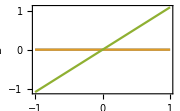
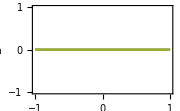
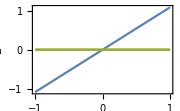

```mathematica
order = 2; (* Desired harmonic order *)
degree = 1; (* Desired harmonic degree *)
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
```

Let us define the known variables in our optimization of saddle coils. Note that our saddle pair is generating an axially symmetric harmonic, so there must be an even number of axial turn ratios and each turn ratio must connect to another with an equal and opposite current flow direction.

```mathematica
curr = {1,-1,1,-1}; (* Axial turn ratios (A) *)
azextents =2; (* Number of azmuthal arcs per saddle *)
χcmin = .1; (* Minimum normalized separation *)
χcmax = 2.56; (* Maximum normalized separation *)
ρc = 10 1*^-2; (* Coil radius (m) *)
```

We will now select the optimal azimuthal extents and axial separations of sets of saddles to maximize the N=2, M=1 field harmonic.

```mathematica
solutions =FindSaddleCoil[curr, {order, degree},azextents,{χcmin,χcmax}]
```

<|AxialSeparations→{{Coilχc[1]→0.2995,Coilχc[2]→0.417035,Coilχc[3]→0.654955,Coilχc[4]→2.5558,DesToErr→13.2438},{Coilχc[1]→0.299514,Coilχc[2]→0.417045,Coilχc[3]→0.654995,Coilχc[4]→2.54896,DesToErr→13.2418},{Coilχc[1]→0.299538,Coilχc[2]→0.417063,Coilχc[3]→0.655069,Coilχc[4]→2.53669,DesToErr→13.2381},{Coilχc[1]→0.299551,Coilχc[2]→0.417072,Coilχc[3]→0.655106,Coilχc[4]→2.5307,DesToErr→13.2361},{Coilχc[1]→0.299573,Coilχc[2]→0.417088,Coilχc[3]→0.655173,Coilχc[4]→2.52024,DesToErr→13.2325},{Coilχc[1]→0.299573,Coilχc[2]→0.417088,Coilχc[3]→0.655174,Coilχc[4]→2.52007,DesToErr→13.2325},{Coilχc[1]→0.299589,Coilχc[2]→0.4171,Coilχc[3]→0.655223,Coilχc[4]→2.51282,DesToErr→13.2299},{Coilχc[1]→0.299595,Coilχc[2]→0.417104,Coilχc[3]→0.655239,Coilχc[4]→2.51045,DesToErr→13.229},{Coilχc[1]→0.299609,Coilχc[2]→0.417115,Coilχc[3]→0.655283,Coilχc[4]→2.50396,DesToErr→13.2265},{Coilχc[1]→0.299623,Coilχc[2]→0.417124,Coilχc[3]→0.655324,Coilχc[4]→2.49811,DesToErr→13.2242}},AzimuthalExtents→{{Coilϕc[1]→0.733038,Coilϕc[2]→1.36136},{Coilϕc[1]→0.10472,Coilϕc[2]→1.15192},{Coilϕc[1]→0.733038,Coilϕc[2]→1.78024}}|>

Here, we’ve identified the sets of axial saddle positions which null the field harmonic orders N=4,6,8 and maximize the ratio of the magnitude of the desired field harmonic of order N=2 to the leading-order error N=10. Simultaneously, we have optimized the azimuthal extent of arcs to null the field harmonic degrees M=3,5,7. This means that, when we evaluate the desired-to-leading-order-magnitude ratio, we evaluate the ratio of the magnitude of the harmonic of order N=2 and degree M=1 to that of order N=10 and degree M=1.

We select the set of saddles which maximize this ratio:

```mathematica
χcopt ={Coilχc[1],Coilχc[2],Coilχc[3],Coilχc[4]} /. solutions[[1,1]]
ϕcopt ={Coilϕc[1],Coilϕc[2]} /. solutions[[2,1]]
```

{0.2995,0.417035,0.654955,2.5558}

{0.733038,1.36136}

Let’s create a plot of the optimal set of saddles on the surface of the coil cylinder.

```mathematica
SaddleCoilPlot[χcopt,ϕcopt,curr,ρc,{order,degree}]
```

Let’s examine each magnetic field component along the x-, y-, and z- axes:

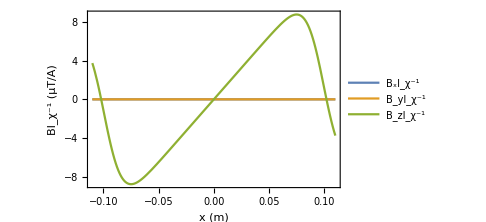
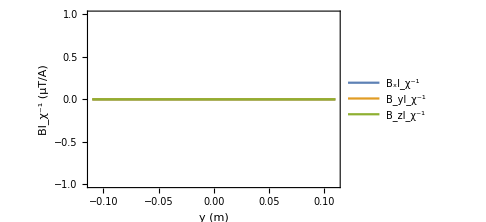
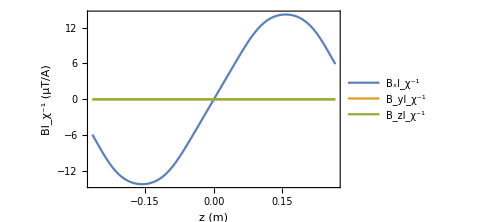

```mathematica
SaddleFieldPlot[χcopt,ϕcopt,curr,ρc,{order,degree}]
```

We can also plot the B_x,B_y,and B_zcomponents of the magnetic field generated by the coils along the xz-plane. Let’s plot them this time with a Blue–Green–Yellow color scheme.

```mathematica
SaddleFieldPlot2D[χcopt,ϕcopt,curr,ρc,{order,degree},ColorFunction->{"BlueGreenYellow"}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Key Options

Optimize only axial separations

```mathematica
FindSaddleCoilAxial[curr, {order, degree},azextents,{χcmin,χcmax},"CoilsReturned"->1]
```

{{Coilχc[1]→0.2995,Coilχc[2]→0.417035,Coilχc[3]→0.654955,Coilχc[4]→2.5558,DesToErr→13.2438}}

Optimize only azimuthal extents

```mathematica
FindSaddleCoilAzimuthal[degree,azextents]
```

{{Coilϕ[1]→0.733038,Coilϕ[2]→1.36136},{Coilϕ[1]→0.10472,Coilϕ[2]→1.15192},{Coilϕ[1]→0.733038,Coilϕ[2]→1.78024}}

## Ellipses

### B_(2,1)

Let us define the known variables in our optimization of ellipse coils.

```mathematica
curr = {1,-1}; (* Turn ratios (A) *)
order = 2; degree = 1;(* Desired harmonic order and degree *)
χcmin = .1; (* Minimum normalized separation *)
χcmax = 1.32; (* Maximum normalized separation *)
ψcmin = .1; (* Minimum normalized elextent *)
ψcmax = .5; (* Maximum normalized extent *)
ρc = 10 1*^-2;(* Coil radius (m) *)
```

We will now select the optimal axial separations and extents of sets of ellipses to maximize the N=2, M=1 field harmonic.

```mathematica
solutions =FindEllipseCoil[curr,{order, degree},{χcmin,χcmax},{ψcmin,ψcmax},
(* Use non-default option values in this case for computational run-time: *)
"MeshPointsPerχc"->8,"ExpansionPointsPerContourDim"->3,"MinSeparationAndExtentDifference"->0]
```

{{Coilχc[1]→0.684225,Coilχc[2]→0.749289,Coilψ[1]→0.284244,Coilψ[2]→0.403639,DesToErr→79233.2},{Coilχc[1]→0.479388,Coilχc[2]→0.578387,Coilψ[1]→0.300762,Coilψ[2]→0.463785,DesToErr→3637.06},{Coilχc[1]→0.537072,Coilχc[2]→0.5746,Coilψ[1]→0.323002,Coilψ[2]→0.384021,DesToErr→1812.49},{Coilχc[1]→0.5073,Coilχc[2]→0.612208,Coilψ[1]→0.276759,Coilψ[2]→0.44532,DesToErr→1523.47},{Coilχc[1]→0.494428,Coilχc[2]→0.509759,Coilψ[1]→0.380522,Coilψ[2]→0.407276,DesToErr→1062.24},{Coilχc[1]→0.593683,Coilχc[2]→0.743838,Coilψ[1]→0.218891,Coilψ[2]→0.472187,DesToErr→1038.07},{Coilχc[1]→0.568439,Coilχc[2]→0.672977,Coilψ[1]→0.252665,Coilψ[2]→0.425128,DesToErr→1032.05},{Coilχc[1]→0.461627,Coilχc[2]→0.551952,Coilψ[1]→0.323995,Coilψ[2]→0.480931,DesToErr→834.544},{Coilχc[1]→0.479132,Coilχc[2]→0.550403,Coilψ[1]→0.328117,Coilψ[2]→0.448515,DesToErr→799.134},{Coilχc[1]→0.591347,Coilχc[2]→0.645635,Coilψ[1]→0.285984,Coilψ[2]→0.376809,DesToErr→717.541}}

Here, we’ve identified the sets of ellipse separations and extents which maximize the ratio of the magnitude of the desired-to-leading-order-error total field harmonic. Specifically, this is the ratio of the field harmonic of order N=2 and degree M=1 compared to that of order N=8 and degree M=1 as the field harmonics of order and degree, {N,M}={{4,1}, {6,1}, {6,3}} are already nulled.

Like before, let’s extract the solution that maximizes this ratio:

```mathematica
χcopt ={Coilχc[1],Coilχc[2]} /. solutions[[1]]
ψcopt ={Coilψc[1],Coilψc[2]} /. solutions[[1]]
```

{0.684225,0.749289}

{0.284244,0.403639}

```mathematica
EllipseCoilPlot[{{χcopt[[1]],ψcopt[[1]]},{χcopt[[2]],ψcopt[[2]]}} ,curr,ρc,{order,degree}]
```

Let’s examine each magnetic field component along the x-, y-, and z- axes:

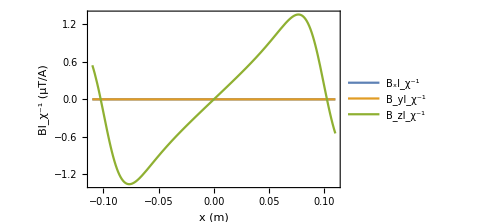
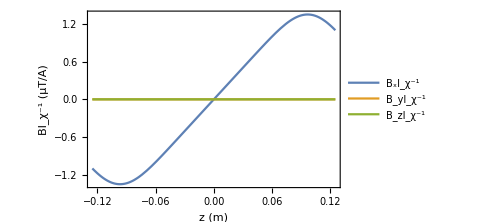
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EllipseFieldPlot[{{χcopt[[1]],ψcopt[[1]]},{χcopt[[2]],ψcopt[[2]]}} ,curr,ρc,{order,degree}]
```

We can also plot the B_x,B_y,and B_zcomponents of the magnetic field generated by the coils along the xz-plane.

```mathematica
EllipseFieldPlot2D[{{χcopt[[1]],ψcopt[[1]]},{χcopt[[2]],ψcopt[[2]]}} ,curr,ρc,{order,degree}]
```

{-Graphics-,-Graphics-,-Graphics-}

## Supplementary Coil Designs

### B_(1,0)

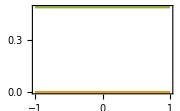
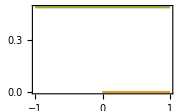
{-Graphics-,-Graphics-,-Graphics-}

{Coilχc[1]→0.453652,Coilχc[2]→0.945434,DesToErr→10.3162}

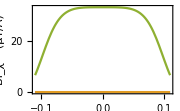
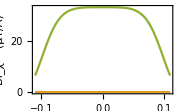
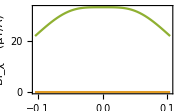

```mathematica
curr = {3,1}; order = 1; degree = 0; χcmin = .1;χcmax = 0.95;ρc = 10 1*^-2;
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
solution =FindLoopCoil[curr, order,{χcmin,χcmax},"CoilsReturned"->1][[1]]
LoopCoilPlot[solution,curr, ρc,order]
LoopFieldPlot[solution,curr, ρc,order, ImageSize->Small]
```

### B_(3,0)

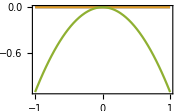
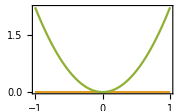
{-Graphics-,-Graphics-,-Graphics-}

{Coilχc[1]→0.377471,Coilχc[2]→0.901987,DesToErr→2265.09}

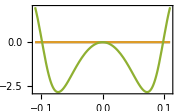
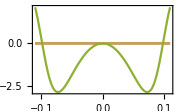
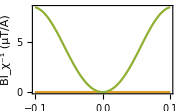

```mathematica
curr = {-1,2}; order = 3; degree=0; χcmin = .1;χcmax = 0.95;ρc = 10 1*^-2;
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
solution =FindLoopCoil[curr, order,{χcmin,χcmax},"CoilsReturned"->1][[1]]
LoopCoilPlot[solution,curr, ρc,order]
LoopFieldPlot[solution,curr, ρc,order, ImageSize->Small]
```

```mathematica
}
```